```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=100;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*
(*Turns off blue and red*)
tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.0 π;
θ3=0.5π;
*)

tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.5 π;
θ3=0.5π;

ϕ=0.5 π;
ϕ3=0;
```

```mathematica
H[θM_]:=Block[{Hsp},
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ12τ11=SparseArray[{Band[{1,1}]->ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];
H3σ21τ11=SparseArray[{Band[{1,1}]->-ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];

H3σ12τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];
H3σ21τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-H3τ11;
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx+1}->tϕ3,{2NxM+NxM/2,2Nx+1}->-tϕ3,{3NxM+NxM/2,3Nx+1}->-tϕ3},{4NxM,4Nx}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];


Hsp
];
```

```mathematica
θM=0.0
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[H[θM],-10]]]];



n=5;
Print[{θM,e[[n]],e[[n-1]]}];
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];




e[[n-1]];
ψB1ue=Table[{i-1,Abs[ψ[[n-1,i]]]},{i,1,Nx}];
ψBMue=Table[{i-1-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx,4Nx+NxM}];
ψB2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψB3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];
```

0.

{0.,-0.0000692569,-0.00118519}

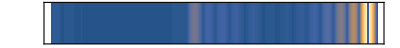

```mathematica
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψbarC=Join[Table[{i,0.0,ψbar[[i,2]]},{i,1,Length[ψbar]}],Table[{i,1.0,ψbar[[i,2]]},{i,1,Length[ψbar]}]];
bar=ListContourPlot[ψbarC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->1/10,FrameTicks->None]
```

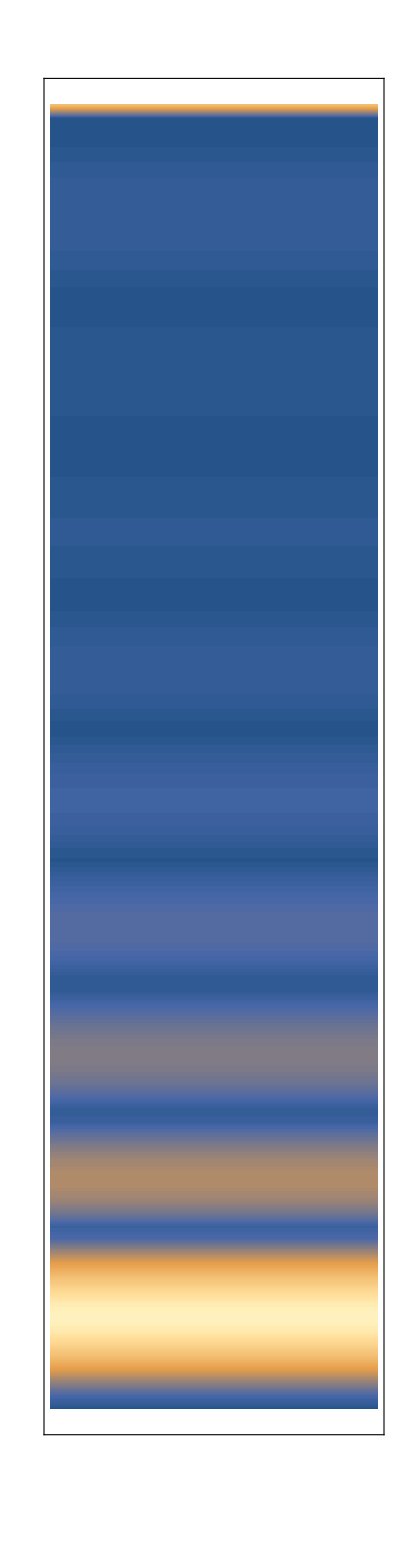

```mathematica
ψleg=ψA3ue;
ψlegC=Join[Table[{0.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}],Table[{1.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}]];
leg=ListContourPlot[ψlegC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->10/1,FrameTicks->None]
```

```mathematica
{e00,ψ00}=Transpose[Sort[Transpose[Eigensystem[H[0.0]]]]];
```

Eigensystem::arh: Because finding 1360 out of the 1360 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
{e14,ψ14}=Transpose[Sort[Transpose[Eigensystem[H[1.4]]]]];
```

Eigensystem::arh: Because finding 1360 out of the 1360 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
n=Length[H[0.0]]/2+1;
e00[[n]]
e00[[n+1]]
Conjugate[ψ00[[n]]].ψ14[[n]]
```

0.0000678457

0.00118407

0.00428496+0.484071 ⅈ

```mathematica
dt=0.1;
ψt = Sum[ⅇ^(-ⅈ e00[[m]] dt)*ψ00[[m]]*Conjugate[ψ00[[m]]].ψ14[[n]],{m,1,Length[e00]}];
```

```mathematica
U00= IdentityMatrix[Length[H[0.0]]]-ⅈ H[0.0]*dt;
ψtt = U00.ψ14[[n]];
```

```mathematica
ψttt = Sum[ⅇ^(-ⅈ e00[[m]] dt)*ψ00[[m]]*Conjugate[ψ00[[m]]].ψ14[[n]],{m,n,Length[e00]}];
ψttt=ψttt/√(ψttt.Conjugate[ψttt]);
```

```mathematica
Conjugate[ψt].ψ14[[n]]
Conjugate[ψtt].ψ14[[n]]
Conjugate[ψttt].ψ14[[n]]
```

0.281445+0.236946 ⅈ

1.-0.0000182831 ⅈ

0.703605+0.000104071 ⅈ

0.703609+0. ⅈ

```mathematica
Table[Conjugate[ψ00[[m]]].ψ14[[n]],{m,n-3,n+3}]
```

{-0.00174327-0.00597661 ⅈ,0.226522-0.434195 ⅈ,0.118798+0.500514 ⅈ,0.00428496+0.484071 ⅈ,-0.351542-0.365365 ⅈ,0.028356+0.0507134 ⅈ,-0.0000686525+0.00179401 ⅈ}

```mathematica
"Using full spectrucm"
n=Length[H[0.0]]/2+1;
dt=0.1;
dθ = dt;
{e00,ψ00}=Transpose[Sort[Transpose[Eigensystem[H[0.0]]]]];
ψ0=ψ00[[n]];
ψt = ψ0;
For[θ=0.0,θ≤2π,θ+=dθ,
Uθ= IdentityMatrix[Length[H[θ]]]-ⅈ H[θ]*dt;
ψtt = Uθ.ψt;
Print[{θ,Conjugate[ψt].ψ0,Abs[Conjugate[ψt].ψ0]^2}];
];
```

Using full spectrucm

Eigensystem::arh: Because finding 1360 out of the 1360 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{0.,1.+0. ⅈ,1.}

{0.1,1.+0. ⅈ,1.}

{0.2,1.+0. ⅈ,1.}

{0.3,1.+0. ⅈ,1.}

{0.4,1.+0. ⅈ,1.}

{0.5,1.+0. ⅈ,1.}

{0.6,1.+0. ⅈ,1.}

{0.7,1.+0. ⅈ,1.}

{0.8,1.+0. ⅈ,1.}

{0.9,1.+0. ⅈ,1.}

{1.,1.+0. ⅈ,1.}

{1.1,1.+0. ⅈ,1.}

{1.2,1.+0. ⅈ,1.}

{1.3,1.+0. ⅈ,1.}

{1.4,1.+0. ⅈ,1.}

{1.5,1.+0. ⅈ,1.}

{1.6,1.+0. ⅈ,1.}

{1.7,1.+0. ⅈ,1.}

{1.8,1.+0. ⅈ,1.}

{1.9,1.+0. ⅈ,1.}

{2.,1.+0. ⅈ,1.}

{2.1,1.+0. ⅈ,1.}

{2.2,1.+0. ⅈ,1.}

{2.3,1.+0. ⅈ,1.}

{2.4,1.+0. ⅈ,1.}

{2.5,1.+0. ⅈ,1.}

{2.6,1.+0. ⅈ,1.}

{2.7,1.+0. ⅈ,1.}

{2.8,1.+0. ⅈ,1.}

{2.9,1.+0. ⅈ,1.}

{3.,1.+0. ⅈ,1.}

{3.1,1.+0. ⅈ,1.}

{3.2,1.+0. ⅈ,1.}

{3.3,1.+0. ⅈ,1.}

{3.4,1.+0. ⅈ,1.}

{3.5,1.+0. ⅈ,1.}

{3.6,1.+0. ⅈ,1.}

{3.7,1.+0. ⅈ,1.}

{3.8,1.+0. ⅈ,1.}

{3.9,1.+0. ⅈ,1.}

{4.,1.+0. ⅈ,1.}

{4.1,1.+0. ⅈ,1.}

{4.2,1.+0. ⅈ,1.}

{4.3,1.+0. ⅈ,1.}

{4.4,1.+0. ⅈ,1.}

{4.5,1.+0. ⅈ,1.}

{4.6,1.+0. ⅈ,1.}

{4.7,1.+0. ⅈ,1.}

{4.8,1.+0. ⅈ,1.}

{4.9,1.+0. ⅈ,1.}

{5.,1.+0. ⅈ,1.}

{5.1,1.+0. ⅈ,1.}

{5.2,1.+0. ⅈ,1.}

{5.3,1.+0. ⅈ,1.}

{5.4,1.+0. ⅈ,1.}

{5.5,1.+0. ⅈ,1.}

{5.6,1.+0. ⅈ,1.}

{5.7,1.+0. ⅈ,1.}

{5.8,1.+0. ⅈ,1.}

{5.9,1.+0. ⅈ,1.}

{6.,1.+0. ⅈ,1.}

{6.1,1.+0. ⅈ,1.}

{6.2,1.+0. ⅈ,1.}

```mathematica
"Using half spectrum"
n=Length[H[0.0]]/2+1;
dt=0.1;
dθ = 0.1dt;
{e00,ψ00}=Transpose[Sort[Transpose[Eigensystem[H[0.0]]]]];
ψ0=ψ00[[n]];
ψt = ψ0;
For[θ=0.0,θ≤2π,θ+=dθ,
{eθ,ψθ}=Transpose[Sort[Transpose[Eigensystem[H[θ]]]]];
ψt=Sum[ⅇ^(-ⅈ eθ[[m]] dt)*ψθ[[m]]*Conjugate[ψθ[[m]]].ψt,{m,n,Length[eθ]}];
ψt=ψt/√(ψt.Conjugate[ψt]);
Print[{θ,Conjugate[ψt].ψ0,Abs[Conjugate[ψt].ψ0]^2}];
];
```

Using half spectrum

Eigensystem::arh: Because finding 1360 out of the 1360 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{0.,1.+6.78457×10^-6 ⅈ,1.}

Eigensystem::arh: Because finding 1360 out of the 1360 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{0.01,0.999973+0.0000135956 ⅈ,0.999946}

Eigensystem::arh: Because finding 1360 out of the 1360 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

{0.02,0.999891+0.0000202386 ⅈ,0.999783}

{0.03,0.999753+0.0000265163 ⅈ,0.999505}

{0.04,0.999555+0.0000322285 ⅈ,0.99911}

{0.05,0.999296+0.0000371709 ⅈ,0.998593}

{0.06,0.998974+0.000041135 ⅈ,0.99795}

{0.07,0.998588+0.0000439085 ⅈ,0.997178}

{0.08,0.998135+0.0000452753 ⅈ,0.996274}

{0.09,0.997614+0.0000450165 ⅈ,0.995234}

{0.1,0.997023+0.0000429111 ⅈ,0.994054}

{0.11,0.99636+0.0000387379 ⅈ,0.992733}

{0.12,0.995624+0.0000322766 ⅈ,0.991267}

{0.13,0.994814+0.0000233094 ⅈ,0.989654}

{0.14,0.993927+0.0000116233 ⅈ,0.987892}

{0.15,0.992964-2.98845×10^-6 ⅈ,0.985978}

{0.16,0.991924-0.0000207244 ⅈ,0.983913}

{0.17,0.990804-0.0000417737 ⅈ,0.981693}

{0.18,0.989606-0.000066314 ⅈ,0.97932}

{0.19,0.988327-0.0000945109 ⅈ,0.976791}

{0.2,0.986969-0.000126517 ⅈ,0.974108}

{0.21,0.98553-0.000162471 ⅈ,0.97127}

{0.22,0.984011-0.000202497 ⅈ,0.968278}

{0.23,0.982412-0.000246705 ⅈ,0.965134}

{0.24,0.980734-0.000295192 ⅈ,0.961839}

{0.25,0.978976-0.000348041 ⅈ,0.958395}

{0.26,0.97714-0.00040532 ⅈ,0.954804}

{0.27,0.975227-0.000467087 ⅈ,0.951069}

{0.28,0.973238-0.000533387 ⅈ,0.947192}

{0.29,0.971174-0.000604253 ⅈ,0.943179}

{0.3,0.969036-0.000679709 ⅈ,0.939031}

{0.31,0.966826-0.00075977 ⅈ,0.934754}

{0.32,0.964547-0.000844439 ⅈ,0.930351}

{0.33,0.962199-0.000933711 ⅈ,0.925828}

{0.34,0.959785-0.00102757 ⅈ,0.921189}

{0.35,0.957308-0.00112601 ⅈ,0.91644}

{0.36,0.954769-0.00122898 ⅈ,0.911585}

{0.37,0.95217-0.00133645 ⅈ,0.90663}

{0.38,0.949516-0.00144837 ⅈ,0.901582}

{0.39,0.946807-0.00156469 ⅈ,0.896445}

{0.4,0.944047-0.00168534 ⅈ,0.891227}

{0.41,0.941238-0.00181025 ⅈ,0.885932}

{0.42,0.938383-0.00193934 ⅈ,0.880567}

{0.43,0.935485-0.00207252 ⅈ,0.875137}

{0.44,0.932547-0.00220971 ⅈ,0.86965}

{0.45,0.929572-0.0023508 ⅈ,0.86411}

{0.46,0.926562-0.0024957 ⅈ,0.858524}

{0.47,0.923521-0.00264429 ⅈ,0.852897}

{0.48,0.92045-0.00279647 ⅈ,0.847236}

{0.49,0.917353-0.00295214 ⅈ,0.841546}

{0.5,0.914233-0.00311117 ⅈ,0.835832}

{0.51,0.911092-0.00327347 ⅈ,0.830099}

{0.52,0.907933-0.00343893 ⅈ,0.824354}

{0.53,0.904758-0.00360744 ⅈ,0.8186}

{0.54,0.90157-0.00377891 ⅈ,0.812842}

{0.55,0.898371-0.00395323 ⅈ,0.807086}

{0.56,0.895163-0.00413031 ⅈ,0.801335}

{0.57,0.89195-0.00431006 ⅈ,0.795593}

{0.58,0.888732-0.00449239 ⅈ,0.789866}

{0.59,0.885513-0.0046772 ⅈ,0.784155}

{0.6,0.882294-0.00486442 ⅈ,0.778466}

{0.61,0.879077-0.00505396 ⅈ,0.772801}

{0.62,0.875863-0.00524573 ⅈ,0.767164}

{0.63,0.872656-0.00543964 ⅈ,0.761558}

{0.64,0.869456-0.00563562 ⅈ,0.755985}

{0.65,0.866264-0.00583358 ⅈ,0.750448}

{0.66,0.863083-0.00603343 ⅈ,0.744949}

{0.67,0.859914-0.00623509 ⅈ,0.739492}

{0.68,0.856759-0.00643846 ⅈ,0.734077}

{0.69,0.853617-0.00664346 ⅈ,0.728707}

{0.7,0.850491-0.00685001 ⅈ,0.723383}

{0.71,0.847382-0.00705801 ⅈ,0.718107}

{0.72,0.844291-0.00726739 ⅈ,0.71288}

{0.73,0.841218-0.00747806 ⅈ,0.707704}

{0.74,0.838165-0.00768994 ⅈ,0.70258}

{0.75,0.835132-0.00790295 ⅈ,0.697508}

{0.76,0.83212-0.00811701 ⅈ,0.69249}

{0.77,0.82913-0.00833206 ⅈ,0.687526}

{0.78,0.826162-0.00854802 ⅈ,0.682617}

{0.79,0.823217-0.00876482 ⅈ,0.677763}

{0.8,0.820295-0.0089824 ⅈ,0.672965}

{0.81,0.817397-0.00920069 ⅈ,0.668222}

{0.82,0.814523-0.00941961 ⅈ,0.663536}

{0.83,0.811674-0.00963911 ⅈ,0.658907}

{0.84,0.808849-0.00985911 ⅈ,0.654334}

{0.85,0.806049-0.0100796 ⅈ,0.649817}

{0.86,0.803275-0.0103004 ⅈ,0.645357}

{0.87,0.800526-0.0105215 ⅈ,0.640953}

{0.88,0.797803-0.0107428 ⅈ,0.636605}

{0.89,0.795105-0.0109643 ⅈ,0.632312}

{0.9,0.792433-0.0111859 ⅈ,0.628075}

{0.91,0.789786-0.0114075 ⅈ,0.623893}

{0.92,0.787166-0.011629 ⅈ,0.619765}

{0.93,0.78457-0.0118505 ⅈ,0.615691}

{0.94,0.782001-0.0120719 ⅈ,0.611671}

{0.95,0.779456-0.0122931 ⅈ,0.607704}

{0.96,0.776937-0.0125141 ⅈ,0.603788}

{0.97,0.774443-0.012735 ⅈ,0.599925}

{0.98,0.771974-0.0129556 ⅈ,0.596112}

{0.99,0.76953-0.0131761 ⅈ,0.59235}

{1.,0.76711-0.0133965 ⅈ,0.588637}

{1.01,0.764715-0.0136168 ⅈ,0.584974}

{1.02,0.762343-0.0138371 ⅈ,0.581359}

{1.03,0.759996-0.0140574 ⅈ,0.577791}

{1.04,0.757672-0.0142778 ⅈ,0.57427}

{1.05,0.755371-0.0144985 ⅈ,0.570796}

{1.06,0.753094-0.0147194 ⅈ,0.567367}

{1.07,0.75084-0.0149408 ⅈ,0.563983}

{1.08,0.748608-0.0151626 ⅈ,0.560644}

{1.09,0.7464-0.0153849 ⅈ,0.55735}

{1.1,0.744214-0.0156079 ⅈ,0.554098}

{1.11,0.74205-0.0158315 ⅈ,0.55089}

{1.12,0.739909-0.0160558 ⅈ,0.547723}

{1.13,0.73779-0.0162808 ⅈ,0.544599}

{1.14,0.735693-0.0165065 ⅈ,0.541517}

{1.15,0.733618-0.0167329 ⅈ,0.538475}

{1.16,0.731565-0.0169598 ⅈ,0.535474}

{1.17,0.729533-0.0171874 ⅈ,0.532513}

{1.18,0.727522-0.0174154 ⅈ,0.529592}

{1.19,0.725533-0.0176439 ⅈ,0.526709}

{1.2,0.723565-0.0178726 ⅈ,0.523865}

{1.21,0.721617-0.0181015 ⅈ,0.521059}

{1.22,0.71969-0.0183304 ⅈ,0.51829}

{1.23,0.717783-0.0185593 ⅈ,0.515557}

{1.24,0.715896-0.018788 ⅈ,0.51286}

{1.25,0.714029-0.0190165 ⅈ,0.510199}

{1.26,0.712181-0.0192446 ⅈ,0.507572}

{1.27,0.710352-0.0194723 ⅈ,0.504978}

{1.28,0.708541-0.0196996 ⅈ,0.502418}

{1.29,0.706748-0.0199264 ⅈ,0.49989}

{1.3,0.704974-0.0201527 ⅈ,0.497394}

{1.31,0.703217-0.0203786 ⅈ,0.494929}

{1.32,0.701477-0.020604 ⅈ,0.492494}

{1.33,0.699753-0.0208292 ⅈ,0.490089}

{1.34,0.698047-0.021054 ⅈ,0.487712}

{1.35,0.696356-0.0212786 ⅈ,0.485364}

{1.36,0.694681-0.0215032 ⅈ,0.483044}

{1.37,0.693022-0.0217278 ⅈ,0.480751}

{1.38,0.691378-0.0219525 ⅈ,0.478485}

{1.39,0.689749-0.0221775 ⅈ,0.476245}

{1.4,0.688135-0.0224028 ⅈ,0.474031}

{1.41,0.686535-0.0226285 ⅈ,0.471843}

{1.42,0.68495-0.0228548 ⅈ,0.469679}

{1.43,0.68338-0.0230817 ⅈ,0.467541}

{1.44,0.681824-0.0233093 ⅈ,0.465427}

{1.45,0.680282-0.0235376 ⅈ,0.463337}

{1.46,0.678753-0.0237666 ⅈ,0.461271}

{1.47,0.677239-0.0239964 ⅈ,0.459228}

{1.48,0.675738-0.0242269 ⅈ,0.457209}

{1.49,0.674251-0.0244582 ⅈ,0.455213}

{1.5,0.672777-0.0246902 ⅈ,0.453239}

{1.51,0.671317-0.0249229 ⅈ,0.451287}

{1.52,0.669869-0.0251563 ⅈ,0.449357}

{1.53,0.668435-0.0253903 ⅈ,0.447449}

{1.54,0.667013-0.0256248 ⅈ,0.445563}

{1.55,0.665604-0.0258599 ⅈ,0.443697}

{1.56,0.664207-0.0260954 ⅈ,0.441851}

{1.57,0.662822-0.0263314 ⅈ,0.440026}

{1.58,0.661449-0.0265678 ⅈ,0.438221}

{1.59,0.660088-0.0268047 ⅈ,0.436435}

{1.6,0.658739-0.0270419 ⅈ,0.434668}

{1.61,0.6574-0.0272795 ⅈ,0.432919}

{1.62,0.656073-0.0275175 ⅈ,0.431189}

{1.63,0.654757-0.027756 ⅈ,0.429477}

{1.64,0.653451-0.0279948 ⅈ,0.427782}

{1.65,0.652156-0.0282341 ⅈ,0.426105}

{1.66,0.650872-0.0284739 ⅈ,0.424445}

{1.67,0.649597-0.0287142 ⅈ,0.422801}

{1.68,0.648332-0.0289551 ⅈ,0.421173}

{1.69,0.647077-0.0291966 ⅈ,0.419561}

{1.7,0.645832-0.0294388 ⅈ,0.417965}

{1.71,0.644596-0.0296817 ⅈ,0.416384}

{1.72,0.643369-0.0299253 ⅈ,0.414819}

{1.73,0.642151-0.0301697 ⅈ,0.413268}

{1.74,0.640942-0.0304149 ⅈ,0.411732}

{1.75,0.639742-0.0306611 ⅈ,0.41021}

{1.76,0.638551-0.0309082 ⅈ,0.408703}

{1.77,0.637368-0.0311563 ⅈ,0.407209}

{1.78,0.636194-0.0314054 ⅈ,0.405729}

{1.79,0.635028-0.0316557 ⅈ,0.404262}

{1.8,0.63387-0.031907 ⅈ,0.402809}

{1.81,0.63272-0.0321596 ⅈ,0.401369}

{1.82,0.631578-0.0324134 ⅈ,0.399941}

{1.83,0.630444-0.0326684 ⅈ,0.398526}

{1.84,0.629317-0.0329248 ⅈ,0.397124}

{1.85,0.628198-0.0331825 ⅈ,0.395734}

{1.86,0.627087-0.0334416 ⅈ,0.394357}

{1.87,0.625983-0.0337022 ⅈ,0.392991}

{1.88,0.624887-0.0339642 ⅈ,0.391637}

{1.89,0.623798-0.0342277 ⅈ,0.390295}

{1.9,0.622716-0.0344927 ⅈ,0.388964}

{1.91,0.621641-0.0347592 ⅈ,0.387645}

{1.92,0.620573-0.0350272 ⅈ,0.386338}

{1.93,0.619512-0.0352968 ⅈ,0.385041}

{1.94,0.618458-0.035568 ⅈ,0.383755}

{1.95,0.61741-0.0358408 ⅈ,0.38248}

{1.96,0.61637-0.0361152 ⅈ,0.381216}

{1.97,0.615336-0.0363911 ⅈ,0.379962}

{1.98,0.614308-0.0366687 ⅈ,0.378719}

{1.99,0.613287-0.036948 ⅈ,0.377486}

{2.,0.612272-0.0372288 ⅈ,0.376263}

{2.01,0.611263-0.0375114 ⅈ,0.37505}

{2.02,0.610261-0.0377957 ⅈ,0.373847}

{2.03,0.609264-0.0380817 ⅈ,0.372653}

{2.04,0.608274-0.0383694 ⅈ,0.371469}

{2.05,0.607289-0.038659 ⅈ,0.370295}

{2.06,0.60631-0.0389503 ⅈ,0.369129}

{2.07,0.605337-0.0392434 ⅈ,0.367973}

{2.08,0.60437-0.0395384 ⅈ,0.366826}

{2.09,0.603408-0.0398353 ⅈ,0.365688}

{2.1,0.602452-0.040134 ⅈ,0.364559}

{2.11,0.601501-0.0404346 ⅈ,0.363438}

{2.12,0.600556-0.040737 ⅈ,0.362327}

{2.13,0.599616-0.0410414 ⅈ,0.361223}

{2.14,0.598681-0.0413476 ⅈ,0.360129}

{2.15,0.597752-0.0416556 ⅈ,0.359042}

{2.16,0.596827-0.0419655 ⅈ,0.357964}

{2.17,0.595908-0.0422772 ⅈ,0.356894}

{2.18,0.594994-0.0425906 ⅈ,0.355832}

{2.19,0.594085-0.0429059 ⅈ,0.354778}

{2.2,0.59318-0.0432229 ⅈ,0.353731}

{2.21,0.59228-0.0435417 ⅈ,0.352692}

{2.22,0.591385-0.0438622 ⅈ,0.35166}

{2.23,0.590494-0.0441845 ⅈ,0.350635}

{2.24,0.589607-0.0445085 ⅈ,0.349617}

{2.25,0.588724-0.0448344 ⅈ,0.348606}

{2.26,0.587845-0.0451622 ⅈ,0.347602}

{2.27,0.586971-0.0454919 ⅈ,0.346604}

{2.28,0.586099-0.0458237 ⅈ,0.345612}

{2.29,0.585232-0.0461576 ⅈ,0.344626}

{2.3,0.584367-0.0464937 ⅈ,0.343647}

{2.31,0.583506-0.0468323 ⅈ,0.342673}

{2.32,0.582648-0.0471733 ⅈ,0.341705}

{2.33,0.581794-0.047517 ⅈ,0.340742}

{2.34,0.580943-0.0478635 ⅈ,0.339785}

{2.35,0.580094-0.048213 ⅈ,0.338834}

{2.36,0.579249-0.0485656 ⅈ,0.337888}

{2.37,0.578407-0.0489214 ⅈ,0.336948}

{2.38,0.577569-0.0492805 ⅈ,0.336014}

{2.39,0.576733-0.0496431 ⅈ,0.335086}

{2.4,0.575901-0.0500091 ⅈ,0.334163}

{2.41,0.575073-0.0503787 ⅈ,0.333247}

{2.42,0.574248-0.0507518 ⅈ,0.332336}

{2.43,0.573427-0.0511285 ⅈ,0.331432}

{2.44,0.572609-0.0515088 ⅈ,0.330534}

{2.45,0.571795-0.0518925 ⅈ,0.329643}

{2.46,0.570985-0.0522795 ⅈ,0.328757}

{2.47,0.570179-0.0526699 ⅈ,0.327878}

{2.48,0.569377-0.0530635 ⅈ,0.327006}

{2.49,0.568579-0.0534602 ⅈ,0.32614}

{2.5,0.567784-0.0538598 ⅈ,0.32528}

{2.51,0.566993-0.0542623 ⅈ,0.324426}

{2.52,0.566206-0.0546676 ⅈ,0.323578}

{2.53,0.565422-0.0550756 ⅈ,0.322736}

{2.54,0.564642-0.0554862 ⅈ,0.321899}

{2.55,0.563865-0.0558994 ⅈ,0.321068}

{2.56,0.563091-0.0563152 ⅈ,0.320243}

{2.57,0.562319-0.0567335 ⅈ,0.319422}

{2.58,0.561551-0.0571545 ⅈ,0.318606}

{2.59,0.560785-0.0575782 ⅈ,0.317795}

{2.6,0.560021-0.0580046 ⅈ,0.316988}

{2.61,0.55926-0.0584339 ⅈ,0.316186}

{2.62,0.5585-0.0588662 ⅈ,0.315388}

{2.63,0.557743-0.0593016 ⅈ,0.314594}

{2.64,0.556987-0.0597402 ⅈ,0.313804}

{2.65,0.556234-0.0601823 ⅈ,0.313018}

{2.66,0.555482-0.0606279 ⅈ,0.312236}

{2.67,0.554732-0.0610772 ⅈ,0.311458}

{2.68,0.553983-0.0615304 ⅈ,0.310683}

{2.69,0.553237-0.0619876 ⅈ,0.309913}

{2.7,0.552492-0.0624488 ⅈ,0.309147}

{2.71,0.551749-0.0629142 ⅈ,0.308385}

{2.72,0.551008-0.0633839 ⅈ,0.307627}

{2.73,0.550269-0.063858 ⅈ,0.306873}

{2.74,0.549532-0.0643364 ⅈ,0.306124}

{2.75,0.548796-0.0648193 ⅈ,0.305379}

{2.76,0.548063-0.0653068 ⅈ,0.304638}

{2.77,0.547332-0.0657987 ⅈ,0.303902}

{2.78,0.546603-0.0662951 ⅈ,0.30317}

{2.79,0.545877-0.0667962 ⅈ,0.302443}

{2.8,0.545152-0.0673017 ⅈ,0.301721}

{2.81,0.54443-0.0678119 ⅈ,0.301002}

{2.82,0.54371-0.0683266 ⅈ,0.300289}

{2.83,0.542992-0.0688458 ⅈ,0.29958}

{2.84,0.542276-0.0693697 ⅈ,0.298876}

{2.85,0.541563-0.0698981 ⅈ,0.298176}

{2.86,0.540851-0.0704311 ⅈ,0.297481}

{2.87,0.540142-0.0709686 ⅈ,0.29679}

{2.88,0.539435-0.0715108 ⅈ,0.296104}

{2.89,0.53873-0.0720575 ⅈ,0.295423}

{2.9,0.538028-0.0726088 ⅈ,0.294746}

{2.91,0.537327-0.0731646 ⅈ,0.294073}

{2.92,0.536628-0.073725 ⅈ,0.293405}

{2.93,0.535932-0.0742899 ⅈ,0.292742}

{2.94,0.535237-0.0748593 ⅈ,0.292083}

{2.95,0.534545-0.0754333 ⅈ,0.291428}

{2.96,0.533854-0.0760117 ⅈ,0.290778}

{2.97,0.533165-0.0765947 ⅈ,0.290132}

{2.98,0.532478-0.0771821 ⅈ,0.28949}

{2.99,0.531792-0.0777741 ⅈ,0.288852}

{3.,0.531108-0.0783706 ⅈ,0.288218}

{3.01,0.530425-0.0789717 ⅈ,0.287587}

{3.02,0.529744-0.0795775 ⅈ,0.286961}

{3.03,0.529064-0.080188 ⅈ,0.286338}

{3.04,0.528384-0.0808032 ⅈ,0.285719}

{3.05,0.527706-0.0814234 ⅈ,0.285104}

{3.06,0.527029-0.0820485 ⅈ,0.284491}

{3.07,0.526353-0.0826787 ⅈ,0.283883}

{3.08,0.525677-0.0833142 ⅈ,0.283277}

{3.09,0.525002-0.0839551 ⅈ,0.282675}

{3.1,0.524328-0.0846014 ⅈ,0.282077}

{3.11,0.523654-0.0852535 ⅈ,0.281482}

{3.12,0.522981-0.0859112 ⅈ,0.28089}

{3.13,0.522309-0.0865749 ⅈ,0.280302}

{3.14,0.521637-0.0872446 ⅈ,0.279717}

{3.15,0.520966-0.0879204 ⅈ,0.279136}

{3.16,0.520296-0.0886023 ⅈ,0.278558}

{3.17,0.519626-0.0892906 ⅈ,0.277984}

{3.18,0.518957-0.0899852 ⅈ,0.277414}

{3.19,0.518289-0.0906862 ⅈ,0.276848}

{3.2,0.517622-0.0913937 ⅈ,0.276285}

{3.21,0.516956-0.0921077 ⅈ,0.275727}

{3.22,0.51629-0.0928282 ⅈ,0.275172}

{3.23,0.515625-0.0935554 ⅈ,0.274621}

{3.24,0.51496-0.0942891 ⅈ,0.274074}

{3.25,0.514296-0.0950296 ⅈ,0.273531}

{3.26,0.513633-0.0957769 ⅈ,0.272992}

{3.27,0.51297-0.0965311 ⅈ,0.272457}

{3.28,0.512308-0.0972922 ⅈ,0.271925}

{3.29,0.511646-0.0980605 ⅈ,0.271397}

{3.3,0.510984-0.0988359 ⅈ,0.270873}

{3.31,0.510322-0.0996188 ⅈ,0.270353}

{3.32,0.509661-0.100409 ⅈ,0.269836}

{3.33,0.509-0.101207 ⅈ,0.269324}

{3.34,0.508339-0.102013 ⅈ,0.268815}

{3.35,0.507678-0.102827 ⅈ,0.268311}

{3.36,0.507018-0.103649 ⅈ,0.26781}

{3.37,0.506358-0.104479 ⅈ,0.267314}

{3.38,0.505698-0.105318 ⅈ,0.266822}

{3.39,0.505038-0.106166 ⅈ,0.266335}

{3.4,0.504379-0.107022 ⅈ,0.265852}

{3.41,0.503721-0.107886 ⅈ,0.265374}

{3.42,0.503063-0.10876 ⅈ,0.264901}

{3.43,0.502406-0.109642 ⅈ,0.264433}

{3.44,0.501749-0.110533 ⅈ,0.26397}

{3.45,0.501094-0.111433 ⅈ,0.263512}

{3.46,0.500438-0.112342 ⅈ,0.263059}

{3.47,0.499784-0.113259 ⅈ,0.262612}

{3.48,0.49913-0.114186 ⅈ,0.262169}

{3.49,0.498476-0.115121 ⅈ,0.261731}

{3.5,0.497823-0.116065 ⅈ,0.261299}

{3.51,0.49717-0.117019 ⅈ,0.260871}

{3.52,0.496517-0.117981 ⅈ,0.260449}

{3.53,0.495864-0.118952 ⅈ,0.260031}

{3.54,0.49521-0.119932 ⅈ,0.259617}

{3.55,0.494557-0.120922 ⅈ,0.259208}

{3.56,0.493902-0.121922 ⅈ,0.258804}

{3.57,0.493246-0.122931 ⅈ,0.258404}

{3.58,0.492589-0.12395 ⅈ,0.258008}

{3.59,0.491932-0.12498 ⅈ,0.257617}

{3.6,0.491272-0.12602 ⅈ,0.25723}

{3.61,0.490612-0.127072 ⅈ,0.256847}

{3.62,0.489949-0.128135 ⅈ,0.256469}

{3.63,0.489285-0.129209 ⅈ,0.256095}

{3.64,0.48862-0.130296 ⅈ,0.255726}

{3.65,0.487953-0.131394 ⅈ,0.255362}

{3.66,0.487284-0.132506 ⅈ,0.255004}

{3.67,0.486614-0.13363 ⅈ,0.25465}

{3.68,0.485942-0.134768 ⅈ,0.254302}

{3.69,0.485269-0.13592 ⅈ,0.25396}

{3.7,0.484595-0.137085 ⅈ,0.253624}

{3.71,0.483919-0.138265 ⅈ,0.253295}

{3.72,0.483242-0.139458 ⅈ,0.252971}

{3.73,0.482564-0.140667 ⅈ,0.252655}

{3.74,0.481885-0.14189 ⅈ,0.252346}

{3.75,0.481205-0.143128 ⅈ,0.252043}

{3.76,0.480523-0.144381 ⅈ,0.251748}

{3.77,0.479841-0.145649 ⅈ,0.251461}

{3.78,0.479157-0.146933 ⅈ,0.251181}

{3.79,0.478472-0.148233 ⅈ,0.250909}

{3.8,0.477786-0.149548 ⅈ,0.250645}

{3.81,0.477099-0.15088 ⅈ,0.250388}

{3.82,0.47641-0.152228 ⅈ,0.25014}

{3.83,0.47572-0.153593 ⅈ,0.2499}

{3.84,0.475028-0.154974 ⅈ,0.249668}

{3.85,0.474334-0.156373 ⅈ,0.249445}

{3.86,0.473638-0.157789 ⅈ,0.24923}

{3.87,0.472939-0.159224 ⅈ,0.249024}

{3.88,0.472239-0.160676 ⅈ,0.248827}

{3.89,0.471536-0.162147 ⅈ,0.248638}

{3.9,0.470831-0.163637 ⅈ,0.248459}

{3.91,0.470123-0.165147 ⅈ,0.248289}

{3.92,0.469413-0.166676 ⅈ,0.248129}

{3.93,0.468699-0.168226 ⅈ,0.247979}

{3.94,0.467983-0.169797 ⅈ,0.247839}

{3.95,0.467263-0.171388 ⅈ,0.247709}

{3.96,0.46654-0.173002 ⅈ,0.24759}

{3.97,0.465815-0.174637 ⅈ,0.247481}

{3.98,0.465085-0.176295 ⅈ,0.247384}

{3.99,0.464353-0.177976 ⅈ,0.247299}

{4.,0.463617-0.179681 ⅈ,0.247226}

{4.01,0.462877-0.18141 ⅈ,0.247165}

{4.02,0.462134-0.183163 ⅈ,0.247116}

{4.03,0.461386-0.184941 ⅈ,0.247081}

{4.04,0.460635-0.186745 ⅈ,0.247059}

{4.05,0.45988-0.188575 ⅈ,0.24705}

{4.06,0.459121-0.190431 ⅈ,0.247056}

{4.07,0.458357-0.192314 ⅈ,0.247076}

{4.08,0.45759-0.194226 ⅈ,0.247112}

{4.09,0.456817-0.196165 ⅈ,0.247163}

{4.1,0.456041-0.198133 ⅈ,0.24723}

{4.11,0.455259-0.20013 ⅈ,0.247313}

{4.12,0.454473-0.202158 ⅈ,0.247414}

{4.13,0.453682-0.204215 ⅈ,0.247531}

{4.14,0.452886-0.206304 ⅈ,0.247667}

{4.15,0.452086-0.208424 ⅈ,0.247822}

{4.16,0.45128-0.210577 ⅈ,0.247996}

{4.17,0.450469-0.212761 ⅈ,0.24819}

{4.18,0.449653-0.214979 ⅈ,0.248404}

{4.19,0.448831-0.217231 ⅈ,0.248639}

{4.2,0.448004-0.219517 ⅈ,0.248895}

{4.21,0.447172-0.221837 ⅈ,0.249174}

{4.22,0.446334-0.224192 ⅈ,0.249476}

{4.23,0.44549-0.226583 ⅈ,0.249801}

{4.24,0.444641-0.229009 ⅈ,0.250151}

{4.25,0.443786-0.231472 ⅈ,0.250525}

{4.26,0.442925-0.233971 ⅈ,0.250925}

{4.27,0.442058-0.236508 ⅈ,0.251351}

{4.28,0.441185-0.239081 ⅈ,0.251804}

{4.29,0.440305-0.241692 ⅈ,0.252284}

{4.3,0.43942-0.244341 ⅈ,0.252792}

{4.31,0.438528-0.247027 ⅈ,0.253329}

{4.32,0.43763-0.249752 ⅈ,0.253896}

{4.33,0.436726-0.252514 ⅈ,0.254493}

{4.34,0.435815-0.255314 ⅈ,0.25512}

{4.35,0.434898-0.258153 ⅈ,0.255779}

{4.36,0.433975-0.261028 ⅈ,0.25647}

{4.37,0.433045-0.263942 ⅈ,0.257193}

{4.38,0.43211-0.266892 ⅈ,0.25795}

{4.39,0.431168-0.269878 ⅈ,0.25874}

{4.4,0.430221-0.272901 ⅈ,0.259565}

{4.41,0.429268-0.275958 ⅈ,0.260424}

{4.42,0.42831-0.279049 ⅈ,0.261318}

{4.43,0.427347-0.282174 ⅈ,0.262248}

{4.44,0.426379-0.28533 ⅈ,0.263213}

{4.45,0.425407-0.288517 ⅈ,0.264213}

{4.46,0.42443-0.291733 ⅈ,0.265249}

{4.47,0.42345-0.294976 ⅈ,0.266321}

{4.48,0.422467-0.298244 ⅈ,0.267428}

{4.49,0.421482-0.301535 ⅈ,0.26857}

{4.5,0.420494-0.304847 ⅈ,0.269747}

{4.51,0.419505-0.308177 ⅈ,0.270958}

{4.52,0.418515-0.311523 ⅈ,0.272202}

{4.53,0.417526-0.314882 ⅈ,0.273478}

{4.54,0.416537-0.31825 ⅈ,0.274786}

{4.55,0.41555-0.321625 ⅈ,0.276125}

{4.56,0.414566-0.325003 ⅈ,0.277492}

{4.57,0.413586-0.328381 ⅈ,0.278887}

{4.58,0.412611-0.331755 ⅈ,0.280309}

{4.59,0.411641-0.33512 ⅈ,0.281754}

{4.6,0.41068-0.338474 ⅈ,0.283222}

{4.61,0.409726-0.341811 ⅈ,0.284711}

{4.62,0.408783-0.345129 ⅈ,0.286218}

{4.63,0.407852-0.348422 ⅈ,0.287741}

{4.64,0.406933-0.351686 ⅈ,0.289278}

{4.65,0.406029-0.354918 ⅈ,0.290826}

{4.66,0.405141-0.358113 ⅈ,0.292384}

{4.67,0.40427-0.361267 ⅈ,0.293948}

{4.68,0.403418-0.364376 ⅈ,0.295516}

{4.69,0.402586-0.367436 ⅈ,0.297085}

{4.7,0.401776-0.370444 ⅈ,0.298653}

{4.71,0.400989-0.373397 ⅈ,0.300218}

{4.72,0.400227-0.37629 ⅈ,0.301776}

{4.73,0.39949-0.379122 ⅈ,0.303326}

{4.74,0.398779-0.38189 ⅈ,0.304864}

{4.75,0.398096-0.384591 ⅈ,0.30639}

{4.76,0.397441-0.387223 ⅈ,0.307901}

{4.77,0.396815-0.389786 ⅈ,0.309396}

{4.78,0.396219-0.392278 ⅈ,0.310871}

{4.79,0.395652-0.394698 ⅈ,0.312327}

{4.8,0.395116-0.397047 ⅈ,0.313762}

{4.81,0.394609-0.399322 ⅈ,0.315175}

{4.82,0.394133-0.401526 ⅈ,0.316564}

{4.83,0.393687-0.403659 ⅈ,0.31793}

{4.84,0.393271-0.405722 ⅈ,0.319272}

{4.85,0.392884-0.407715 ⅈ,0.320589}

{4.86,0.392526-0.409641 ⅈ,0.321882}

{4.87,0.392197-0.4115 ⅈ,0.323151}

{4.88,0.391895-0.413296 ⅈ,0.324395}

{4.89,0.391621-0.415029 ⅈ,0.325616}

{4.9,0.391372-0.416703 ⅈ,0.326814}

{4.91,0.39115-0.418319 ⅈ,0.327989}

{4.92,0.390952-0.41988 ⅈ,0.329142}

{4.93,0.390778-0.421388 ⅈ,0.330275}

{4.94,0.390627-0.422845 ⅈ,0.331388}

{4.95,0.390499-0.424254 ⅈ,0.332481}

{4.96,0.390392-0.425618 ⅈ,0.333557}

{4.97,0.390306-0.426938 ⅈ,0.334615}

{4.98,0.39024-0.428217 ⅈ,0.335658}

{4.99,0.390193-0.429458 ⅈ,0.336685}

{5.,0.390165-0.430661 ⅈ,0.337698}

{5.01,0.390154-0.431831 ⅈ,0.338698}

{5.02,0.39016-0.432967 ⅈ,0.339685}

{5.03,0.390183-0.434073 ⅈ,0.340662}

{5.04,0.390221-0.43515 ⅈ,0.341628}

{5.05,0.390274-0.4362 ⅈ,0.342584}

{5.06,0.390342-0.437224 ⅈ,0.343532}

{5.07,0.390423-0.438225 ⅈ,0.344471}

{5.08,0.390518-0.439203 ⅈ,0.345404}

{5.09,0.390625-0.44016 ⅈ,0.346329}

{5.1,0.390745-0.441098 ⅈ,0.347249}

{5.11,0.390876-0.442017 ⅈ,0.348163}

{5.12,0.391019-0.442919 ⅈ,0.349073}

{5.13,0.391172-0.443805 ⅈ,0.349978}

{5.14,0.391335-0.444676 ⅈ,0.350879}

{5.15,0.391508-0.445532 ⅈ,0.351778}

{5.16,0.391691-0.446376 ⅈ,0.352673}

{5.17,0.391883-0.447207 ⅈ,0.353567}

{5.18,0.392084-0.448027 ⅈ,0.354458}

{5.19,0.392293-0.448837 ⅈ,0.355349}

{5.2,0.39251-0.449637 ⅈ,0.356238}

{5.21,0.392735-0.450428 ⅈ,0.357126}

{5.22,0.392968-0.45121 ⅈ,0.358015}

{5.23,0.393208-0.451985 ⅈ,0.358903}

{5.24,0.393455-0.452753 ⅈ,0.359792}

{5.25,0.393709-0.453514 ⅈ,0.360682}

{5.26,0.39397-0.454269 ⅈ,0.361573}

{5.27,0.394237-0.455019 ⅈ,0.362465}

{5.28,0.39451-0.455764 ⅈ,0.36336}

{5.29,0.39479-0.456505 ⅈ,0.364256}

{5.3,0.395076-0.457241 ⅈ,0.365154}

{5.31,0.395367-0.457974 ⅈ,0.366055}

{5.32,0.395665-0.458703 ⅈ,0.366959}

{5.33,0.395968-0.45943 ⅈ,0.367866}

{5.34,0.396277-0.460154 ⅈ,0.368777}

{5.35,0.396591-0.460875 ⅈ,0.36969}

{5.36,0.39691-0.461595 ⅈ,0.370607}

{5.37,0.397235-0.462313 ⅈ,0.371529}

{5.38,0.397565-0.463029 ⅈ,0.372454}

{5.39,0.397899-0.463744 ⅈ,0.373383}

{5.4,0.398239-0.464459 ⅈ,0.374316}

{5.41,0.398584-0.465172 ⅈ,0.375254}

{5.42,0.398933-0.465885 ⅈ,0.376196}

{5.43,0.399288-0.466597 ⅈ,0.377143}

{5.44,0.399646-0.467309 ⅈ,0.378095}

{5.45,0.40001-0.468021 ⅈ,0.379051}

{5.46,0.400377-0.468733 ⅈ,0.380012}

{5.47,0.400749-0.469445 ⅈ,0.380979}

{5.48,0.401125-0.470158 ⅈ,0.38195}

{5.49,0.401505-0.470871 ⅈ,0.382926}

{5.5,0.401889-0.471585 ⅈ,0.383907}

{5.51,0.402277-0.472299 ⅈ,0.384894}

{5.52,0.402669-0.473015 ⅈ,0.385885}

{5.53,0.403064-0.473731 ⅈ,0.386882}

{5.54,0.403463-0.474449 ⅈ,0.387884}

{5.55,0.403865-0.475168 ⅈ,0.388892}

{5.56,0.404271-0.475889 ⅈ,0.389905}

{5.57,0.40468-0.47661 ⅈ,0.390923}

{5.58,0.405092-0.477334 ⅈ,0.391947}

{5.59,0.405508-0.478059 ⅈ,0.392977}

{5.6,0.405926-0.478786 ⅈ,0.394012}

{5.61,0.406348-0.479514 ⅈ,0.395052}

{5.62,0.406772-0.480245 ⅈ,0.396098}

{5.63,0.407199-0.480977 ⅈ,0.39715}

{5.64,0.407629-0.481711 ⅈ,0.398207}

{5.65,0.408061-0.482448 ⅈ,0.39927}

{5.66,0.408496-0.483186 ⅈ,0.400338}

{5.67,0.408934-0.483926 ⅈ,0.401411}

{5.68,0.409373-0.484668 ⅈ,0.40249}

{5.69,0.409815-0.485412 ⅈ,0.403574}

{5.7,0.41026-0.486158 ⅈ,0.404662}

{5.71,0.410706-0.486905 ⅈ,0.405756}

{5.72,0.411154-0.487655 ⅈ,0.406855}

{5.73,0.411604-0.488406 ⅈ,0.407958}

{5.74,0.412056-0.489158 ⅈ,0.409066}

{5.75,0.412509-0.489912 ⅈ,0.410178}

{5.76,0.412963-0.490668 ⅈ,0.411293}

{5.77,0.413419-0.491424 ⅈ,0.412413}

{5.78,0.413875-0.492181 ⅈ,0.413535}

{5.79,0.414333-0.49294 ⅈ,0.414661}

{5.8,0.414791-0.493698 ⅈ,0.41579}

{5.81,0.415249-0.494458 ⅈ,0.416921}

{5.82,0.415708-0.495217 ⅈ,0.418053}

{5.83,0.416167-0.495977 ⅈ,0.419188}

{5.84,0.416625-0.496736 ⅈ,0.420323}

{5.85,0.417083-0.497495 ⅈ,0.42146}

{5.86,0.41754-0.498253 ⅈ,0.422596}

{5.87,0.417996-0.49901 ⅈ,0.423732}

{5.88,0.418451-0.499766 ⅈ,0.424867}

{5.89,0.418904-0.500519 ⅈ,0.426}

{5.9,0.419355-0.501271 ⅈ,0.427131}

{5.91,0.419804-0.50202 ⅈ,0.42826}

{5.92,0.420251-0.502766 ⅈ,0.429384}

{5.93,0.420695-0.503508 ⅈ,0.430505}

{5.94,0.421136-0.504246 ⅈ,0.43162}

{5.95,0.421573-0.50498 ⅈ,0.432728}

{5.96,0.422006-0.505709 ⅈ,0.43383}

{5.97,0.422435-0.506431 ⅈ,0.434924}

{5.98,0.422859-0.507148 ⅈ,0.436009}

{5.99,0.423279-0.507857 ⅈ,0.437084}

{6.,0.423692-0.508559 ⅈ,0.438147}

{6.01,0.4241-0.509252 ⅈ,0.439198}

{6.02,0.424501-0.509936 ⅈ,0.440235}

{6.03,0.424895-0.510609 ⅈ,0.441258}

{6.04,0.425282-0.511272 ⅈ,0.442264}

{6.05,0.42566-0.511923 ⅈ,0.443252}

{6.06,0.42603-0.512561 ⅈ,0.44422}

{6.07,0.426392-0.513185 ⅈ,0.445168}

{6.08,0.426743-0.513794 ⅈ,0.446094}

{6.09,0.427084-0.514387 ⅈ,0.446995}

{6.1,0.427415-0.514963 ⅈ,0.44787}

{6.11,0.427734-0.515521 ⅈ,0.448718}

{6.12,0.428041-0.516059 ⅈ,0.449536}

{6.13,0.428336-0.516576 ⅈ,0.450322}

{6.14,0.428617-0.517072 ⅈ,0.451076}

{6.15,0.428884-0.517544 ⅈ,0.451793}

{6.16,0.429137-0.517991 ⅈ,0.452473}

{6.17,0.429375-0.518412 ⅈ,0.453114}

{6.18,0.429597-0.518806 ⅈ,0.453713}

{6.19,0.429802-0.51917 ⅈ,0.454267}

{6.2,0.42999-0.519504 ⅈ,0.454776}

{6.21,0.430161-0.519805 ⅈ,0.455236}

{6.22,0.430313-0.520073 ⅈ,0.455645}

{6.23,0.430446-0.520306 ⅈ,0.456002}

{6.24,0.430559-0.520502 ⅈ,0.456303}

{6.25,0.430652-0.520659 ⅈ,0.456547}

{6.26,0.430723-0.520776 ⅈ,0.456731}

{6.27,0.430774-0.520852 ⅈ,0.456853}

{6.28,0.430802-0.520884 ⅈ,0.456911}

```mathematica
Conjugate[ψt].ψt
```

1.+0. ⅈ